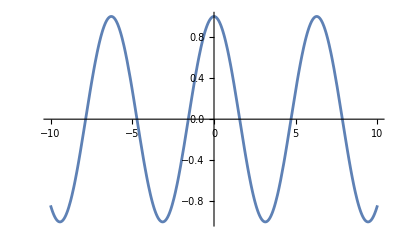

```mathematica
f[x_]:=Cos[x];
range={-10, 10, 0.01};

Plot[f[x], {x, range[[1]], range[[2]]},PlotRange->All]
```

```mathematica
fundemental=.1;
fourier[coef_][x_]:=coef.Table[Cos[2 Pi fundemental(freq-1) x]/Length[coef], {freq, Length[coef]}]
```

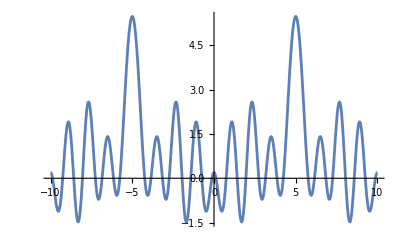

```mathematica
p=RandomReal[{range[[1]], range[[2]]}, {10}];
Plot[fourier[p][x], {x, range[[1]], range[[2]]},PlotRange->All]
```

```mathematica
error[func_]:=NIntegrate[(f[x]-func[x])^2, {x, range[[1]], range[[2]]}]
RepeatedTiming[errorInt[fourier[p]]]
```

{1.52533×10^-7,errorInt[fourier[{7.7238,-9.88443,4.30868,-8.55324,7.0318,-7.52458,0.225615,-8.43039,9.02689,8.01201}]]}

```mathematica
progressMap[func_,l_List, message_:"Complete"]:=Module[{progress=PrintTemporary["0% "<>message]}, Table[NotebookDelete[progress];progress=PrintTemporary[ToString[Round[100*i/Length[l]]]<>"% "<>message]; func[l[[i]]],{i, Length[l]}]]
```

```mathematica
gridGradientDescentOriginal[loss_, ranges_, n_:100, temp_:.05, d_:.01]:=(
indices=Flatten[Table@@Prepend[ranges, ranges[[All, 1]]], Length[ranges]-1];
vals=progressMap[GradientDescent[loss, #, n, temp,d]&,indices, "Of Descents Calculated"];
losses=loss/@vals;
bestI=First[PositionSmallest[losses]];
vals[[bestI]])
```

```mathematica
GradientDescent[loss_, initialValue_List, n_:100, temp_:.05, d_:.01]:=Module[{val=initialValue}, Table[val-=temp((loss[val+#]&/@(d IdentityMatrix[Length[val]]))-loss[val])/d;, {i, n}]; val]
GridGradientDescent[loss_, ranges_, n_:100, temp_:.05, d_:.01]:=
#[[First[PositionSmallest[loss/@#]]]]&[progressMap[GradientDescent[loss, #, n, temp,d]&,Flatten[Table@@Prepend[ranges, ranges[[All, 1]]], Length[ranges]-1], "Of Descents Calculated"]]
```

```mathematica
timesCalled=0;
gridGradientDescent[(timesCalled+=1;#[[1]]^2+#[[2]]^4)&, {{x, -1, 1,1}, {y, -1, 1, 1}}, 100]
timesCalled
```

{-0.00497331,-4.99506×10^-6}

2709

```mathematica
timesCalled=0;
GradientDescent[(timesCalled+=1;#[[1]]^2+#[[2]]^4)&, -{1, 2}]
timesCalled
```

{-0.00502643,-0.151991}

300

```mathematica
sol=GradientDescent[error[fourier[#]]&, {0, 0, 0, 0}]
```

{-0.222608,-0.72297,0.745317,0.165208}

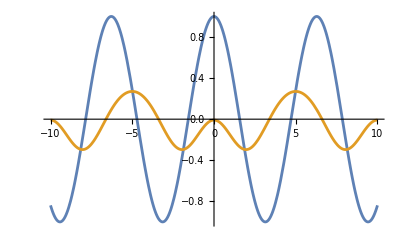

```mathematica
Plot[{f[x], fourier[sol][x]}, {x, -10, 10}]
```